```mathematica
f[x_]:=Sin[2x]Cos[x]-x
```

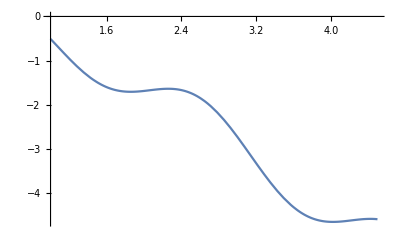

{-1.70409,{x→1.85935}}

```mathematica
Plot[f[x],{x,1,4.5}]
FindMinimum[f[x],{x,1,4.5}]
```

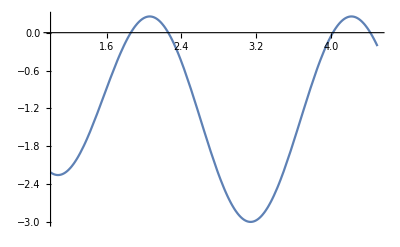

```mathematica
Plot[f'[x],{x,1,4.5}]
```

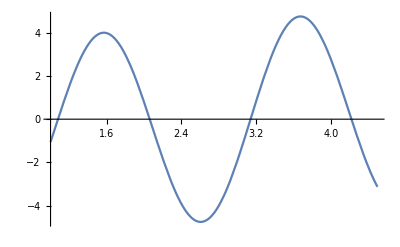

```mathematica
Plot[f''[x],{x,1,4.5}]
```

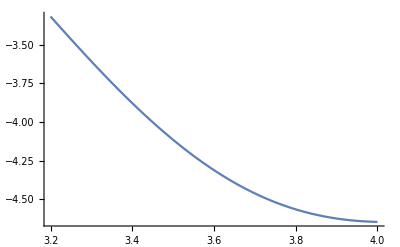

{-4.64738,{x→4.02291}}

```mathematica
Plot[f[x],{x,3.2,4}]
FindMinimum[f[x],{x,3.2,4}]
4.022910252202408
-4.647375604539906
```

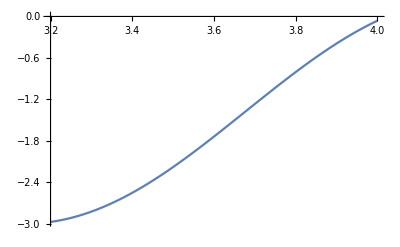

```mathematica
Plot[f'[x],{x, 3.2,4}]
```

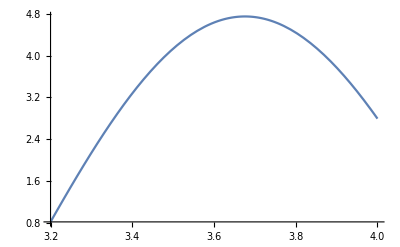

```mathematica
Plot[f''[x],{x,3.2,4}]
```

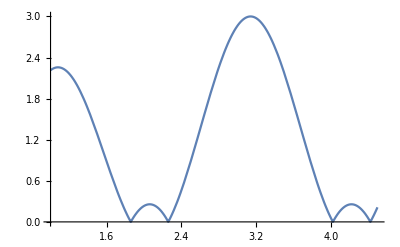

{3.,{x→3.14159}}

```mathematica
Plot[Abs[f'[x]],{x,1, 4.5}]
FindMaximum[Abs[f'[x]],{x,2.5,4}]
```

```mathematica
Limit[f[x],x-> Infinity]
```

-∞

```mathematica
y[x_]:=Sin[2x]Cos[x]
```

```mathematica
Limit[y[x],x-> Infinity]
```

Indeterminate

```mathematica
Limit[Series[Sin[2x]Cos[x]-x,{x,0,12}],x->Infinity]
```

-∞

```mathematica
1.8593488952846022 - 1.8593486896328302
```

2.05652×10^-7

```mathematica
1.8593488952846022/1.8593486896328302
```

1.

```mathematica
4.022910252202408 - 4.0229102876167175
```

-3.54143×10^-8

```mathematica
4.022910252202408/4.0229102876167175
```

1.

```mathematica
f'[x]
```

-1+2 Cos[x] Cos[2 x]-Sin[x] Sin[2 x]

```mathematica
N[ArcCot[-Sqrt[5]]]
```

-0.420534

```mathematica
f[0.4205343352839651]
```

0.259879

```mathematica
N[ArcCos[N[Solve[6 x^3-4x-1==0,x]]]]
```

{{ArcCos[x→-0.636135]},{ArcCos[x→-0.284565]},{ArcCos[x→0.9207]}}

```mathematica
ArcCos[0.9206999328094083]
```

0.400926

```mathematica
f''[x]
```

-4 Cos[2 x] Sin[x]-5 Cos[x] Sin[2 x]

```mathematica
N[ArcCos[-Sqrt[2]/3]]
```

2.06168

```mathematica
f[1.85]
```

-1.70398

```mathematica
f[4.02]
```

-4.64736